```mathematica
DSolve[{
m x''[t]==-f x'[t]/(√(x'[t]^2+y'[t]^2)),
m y''[t]==m g-f y'[t]/(√(x'[t]^2+y'[t]^2))
},{x,y},t]
```

```mathematica
NDSolve[{
x[0]==0,
y[0]==0,
m x''[t]==-f x'[t]/(√(x'[t]^2+y'[t]^2)),
m y''[t]==m g-f y'[t]/(√(x'[t]^2+y'[t]^2))
},{x,y},t]
```

NDSolve::ndlim: Range specification t is not of the form {x, xend} or {x, xmin, xmax}.

NDSolve::ndnco: The number of constraints (2) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (4).

NDSolve[{x[0]==0,y[0]==0,m x''[t]==-(f x'[t])/(√(x'[t]^2+y'[t]^2)),m y''[t]==g m-(f y'[t])/(√(x'[t]^2+y'[t]^2))},{x,y},t]

```mathematica
m=2;
v0=2;
g=10;
f=1;
sol=NDSolve[{
x[0]==0,
y[0]==0,
x'[0]==v0,
y'[0]==0,
m x''[t]==-f x'[t]/(√(x'[t]^2+y'[t]^2)),
m y''[t]==m g-f y'[t]/(√(x'[t]^2+y'[t]^2))
},
{x,y},
{t,0,10}
]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

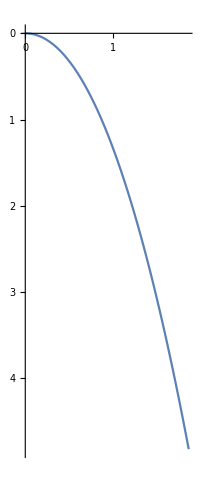

```mathematica
ParametricPlot[
{(x/.sol[[1]])[t],(y/.sol[[1]])[t]},
{t,0,1},
ScalingFunctions->{Automatic,"Reverse"}
]
```

```mathematica
Manipulate[
Module[{sol},
sol=NDSolve[{
x[0]==0,
y[0]==0,
x'[0]==v0,
y'[0]==0,
m x''[t]==-f x'[t]/(√(x'[t]^2+y'[t]^2)),
m y''[t]==m g-f y'[t]/(√(x'[t]^2+y'[t]^2))
},
{x,y},
{t,0,10}
];
ParametricPlot[
{(x/.sol[[1]])[t],(y/.sol[[1]])[t]},
{t,0,1},
ScalingFunctions->{Automatic,"Reverse"}
]
],
{m,0.1,10},
{v0,0.1,10},
{f,0.1,10},
{g,9,10}
]
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {True,y[0]==0,False,y'[0]==0,0.2==-(0.2 t)/(√(4 t^2+y'[t]^2)),0.1 y''[t]==0.9-(0.1 y'[t])/(√(4 Power[«2»]+((«1»)^(«1»)[«1»])^2))}.

ReplaceAll::reps: {True,y[0]==0,False,y'[0]==0,0.2==-(4.08163×10^-6)/(√(1.66597×10^-9+y'[0.0000204082]^2)),0.1 y''[0.0000204082]==0.9-(0.1 y'[0.0000204082])/(√(1.66597×10^-9+((«1»)^(«1»)[«1»])^2))} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {True,y[0]==0,False,y'[0]==0,0.2==-(4.08163×10^-6)/(√(1.66597×10^-9+y'[0.0000204082]^2)),0.1 y''[0.0000204082]==0.9-(0.1 y'[0.0000204082])/(√(1.66597×10^-9+((«1»)^(«1»)[«1»])^2))} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {True,y[0.]==0.,False,y'[0.]==0.,0.2==-(4.08163×10^-6)/(√(1.66597×10^-9+y'[0.0000204082]^2)),0.1 y''[0.0000204082]==0.9-(0.1 y'[0.0000204082])/(√(1.66597×10^-9+((«1»)^(«1»)[«1»])^2))} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

```mathematica
DSolve[{
x[0]==0,
y[0]==0,
x'[0]==v0,
y'[0]==0,
x''[0]==0,
y''[0]==g Sin[a],
x''[t]==-(u g Cos[a] x'[t])/(√(x'[t]^2+y'[t]^2)),
y''[t]==-(u g Cos[a] y'[t])/(√(x'[t]^2+y'[t]^2))+g Sin[a],
(y'[t]/(√(x'[t]^2+y'[t]^2)))^2+(x'[t]/(√(x'[t]^2+y'[t]^2)))^2==1
},{x[t],y[t]},t]
```

```mathematica
v0=2;
m=2;
g=10;
u=1;
a=2;
sol=NDSolve[{
x[0]==0,
y[0]==0,
x'[0]==v0,
y''[0]==g Sin[a],
x''[t]==-(u g Cos[a] x'[t])/(√(x'[t]^2+y'[t]^2)),
y''[t]==-(u g Cos[a] y'[t])/(√(x'[t]^2+y'[t]^2))+g Sin[a]
},
{x,y},{t,0,10}
]
```

```mathematica
Manipulate[
Module[{sol},
sol=NDSolve[{
x[0]==0,
y[0]==0,
x'[0]==v0,
y''[0]==g Sin[a],
x''[t]==-(u g Cos[a] x'[t])/(√(x'[t]^2+y'[t]^2)),
y''[t]==-(u g Cos[a] y'[t])/(√(x'[t]^2+y'[t]^2))+g Sin[a]
},
{x,y},{t,0,10}
];
ParametricPlot[
{(x/.sol[[1]])[t],(y/.sol[[1]])[t]},
{t,0,1},
ScalingFunctions->{Automatic,"Reverse"}
]
],
{m,0.1,10},
{v0,0.1,10},
{f,0.1,10},
{g,9,10},
{a,0.1,10}
]
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {True,y[0]==0,False,y''[0]==0.898501,2==-(17.9101 t u)/(√(4 t^2+y'[t]^2)),y''[t]==0.898501-(8.95504 u y'[t])/(√(4 Power[«2»]+((«1»)^(«1»)[«1»])^2))}.

ReplaceAll::reps: {True,y[0]==0,False,y''[0]==0.898501,2==-(0.000365512 u)/(√(1.66597×10^-9+y'[0.0000204082]^2)),y''[0.0000204082]==0.898501-(8.95504 u y'[0.0000204082])/(√(1.66597×10^-9+((«1»)^(«1»)[«1»])^2))} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {True,y[0]==0,False,y''[0]==0.898501,2==-(0.000365512 u)/(√(1.66597×10^-9+y'[0.0000204082]^2)),y''[0.0000204082]==0.898501-(8.95504 u y'[0.0000204082])/(√(1.66597×10^-9+((«1»)^(«1»)[«1»])^2))} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {True,y[0.]==0.,False,y''[0.]==0.898501,2.==-(0.000365512 u)/(√(1.66597×10^-9+y'[0.0000204082]^2)),y''[0.0000204082]==0.898501-(8.95504 u y'[0.0000204082])/(√(1.66597×10^-9+((«1»)^(«1»)[«1»])^2))} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

```mathematica
Clear["`*"]
```

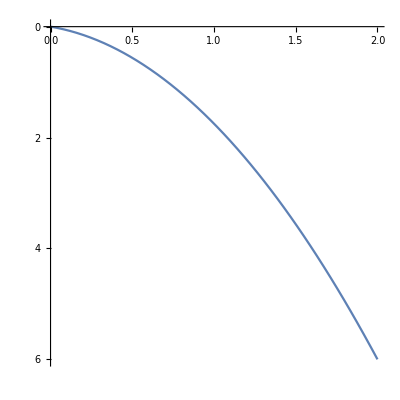
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
Module[{g=10,v0=2,m=2,a=π/2,sol},
sol=NDSolve[{
x[0]==0,
y[0]==0,
x'[0]==v0,
y''[0]==g Sin[a],
x''[t]==-(u g Cos[a] x'[t])/(√(x'[t]^2+y'[t]^2)),
y''[t]==-(u g Cos[a] y'[t])/(√(x'[t]^2+y'[t]^2))+g Sin[a]
},{x,y},{t,0,10}];
ParametricPlot[{(x/.sol⟦1⟧)[t],(y/.sol⟦1⟧)[t]},{t,0,1},
ScalingFunctions->{Automatic,"Reverse"},
AspectRatio->1,
PlotRange->{{0,2},Automatic}]],
{u,0.1,1,0.1}
]
```

```mathematica
plot[v0_,g_,a_,u_]:=Module[{sol,vu},
vu=u;
If[u<=Tan[a]/g,
sol=NDSolve[{
x[0]==0,
y[0]==0,
x'[0]==v0,
y''[0]==g Sin[a],
x''[t]==-(vu g Cos[a] x'[t])/(√(x'[t]^2+y'[t]^2)),
y''[t]==-(vu g Cos[a] y'[t])/(√(x'[t]^2+y'[t]^2))+g Sin[a]},
{x,y},{t,0,5},
MaxSteps->Infinity
];
ParametricPlot[
{(x/.sol⟦1⟧)[t],(y/.sol⟦1⟧)[t]},
{t,0,5},
ScalingFunctions->{Automatic,"Reverse"},
PlotRange->{{0,20},{0,-10}}
]
,
"u">Tan[a]/g"!"
]
];
Manipulate[
plot[v0,g,a,u],
{v0,0.1,10},{g,9,10},{a,0.1,Pi/2},{u,0,1},
SynchronousUpdating->False,
SaveDefinitions->True
]
```

```mathematica
Slider
```

```mathematica
Manipulate[
{Slider[Dynamic[n]],
n},
{a,1,2}
]
```

```mathematica
Manipulate[v+t,Row[{Control@{v,0,1},Control@{t,0,1}}],
ControlPlacement->Left,ControlType->VerticalSlider]
```

```mathematica
Manipulate[value[a,b,c,d,e,f,g,h,i],Style["Matrix values",12,Bold],Grid[{{Control@{{a,0},InputField,ImageSize->Small},Control@{{b,0},InputField,ImageSize->Small}},{Control@{{c,0},InputField,ImageSize->Small},Control@{{d,0},InputField,ImageSize->Small}}}],{{e,-10,"x-min"},-20,0,1},{{f,10,"x-max"},0,20,1},{{g,-10,"y-min"},-20,0,1},{{h,10,"y-max"},0,20,1},{{i,5,"Solutions"},0,50,1}]
```

```mathematica
plot[v0_, g_, a_, u_] := Module[{sol, vu}, 
    vu = u; If[u <= Tan[a]/g, sol = NDSolve[{x[0] == 0, y[0] == 0, 
          Derivative[1][x][0] == v0, Derivative[2][y][0] == g*Sin[a], 
          Derivative[2][x][t] == -((vu*g*Cos[a]*Derivative[1][x][t])/
             Sqrt[Derivative[1][x][t]^2 + Derivative[1][y][t]^2]), 
          Derivative[2][y][t] == -((vu*g*Cos[a]*Derivative[1][y][t])/
              Sqrt[Derivative[1][x][t]^2 + Derivative[1][y][t]^2]) + g*Sin[a]}, {x, y}, 
         {t, 0, 5}, MaxSteps -> Infinity]; ParametricPlot[{(x /. sol[[1]])[t], 
         (y /. sol[[1]])[t]}, {t, 0, 5}, ScalingFunctions -> {Automatic, "Reverse"}, 
        PlotRange -> {{0, 20}, {0, -10}}], "u" > (Tan[a]/g)*"!"]]; 
Manipulate[plot[v0, g, a, u], {v0, 0.1, 10}, {g, 9, 10}, {a, 0.1, Pi/2}, {u, 0, 1}, 
  SynchronousUpdating -> False]
```

```mathematica
//FullForm//Compress
```

1:eJzdVltu1DAUTd8UJIToCroApIENoNLpoEgtipKyAJNxBgvHTv0ICTspO2F11NfO0xNoBiQ+yMdV7Bzfx7l3fOb8E4+zvSAI5BNjVprSFRd5dgI7T425QYwUmiKFs0PYA1NQruS+eSkXEo5urEXW6uyghV0T2cLE93t4frwl4NODWBfk1NhffUXd+Qz8ySNjbkmOpVtC5jFShDNECeCJ3QYTkQl3mgQAglfnAL7GmmJ5Zl6SmqWfBWdcy4/F2rhlGxtwhajEDv+swS8xRTVey+dmHTKiiIn/zSbicFBOglUDGxPoEMBzhJTCgjVUZUFb4TuK2JdtmKVrFgrNQulJ1DH0nq9NkT1FlkBLJ6cuW+0+vjTmkucF12x9VRUCS9lxcOA4aPDDGYGdMHMo6P61OXZ1pw3NDuS1eq/1dova8jpExL9i0QzST/PMT6spx/UGqPmwTDgtcXY8rLqPZBN0uYCp3CgF3ShNYOrfY3pj52WJBSnNDJWYeFHaAdnJx/44C4/UZpg6ahOyRe1OQSprlRdl0JK+nYfjRAbjMcjnkssmn7lM+QnYyXBnIGJyJ1Q/0BHVcgo6P5At/Q9d1AMXHkW7dXZY83ZZ/7oF9f/Rgjm/j5GquHTqCb1R7gI4Crb0BpTrBlWJwoW0i5BlxAhJ7XoDuhIhgXKsBEmjTjW6a6mXMKgwxgVFKb6g7gatBiwj0V11ffWPnK8fP79LrS+Av9QoJNusNEtBJaVHI6jAhVY8N21KkxObUmkuduy5OrWDw1WM2MbTp/EqhJQWIey9WUx+ggpevV700vheYPNnRySTGvQXkmQdnj8AyaPeEw==

```mathematica
Uncompress[]
```

Manipulate[plot[v0,g,a,u],List[v0,0.1,10],List[g,9,10],List[a,0.1,Times[Rational[1,2],Pi]],List[u,0,1],Rule[SynchronousUpdating,False],RuleDelayed[Initialization,SetDelayed[plot[Pattern[v0,Blank[]],Pattern[g,Blank[]],Pattern[a,Blank[]],Pattern[u,Blank[]]],Module[List[sol,vu],CompoundExpression[Set[vu,u],If[LessEqual[u,Times[Tan[a],Power[g,-1]]],CompoundExpression[Set[sol,NDSolve[List[Equal[x[0],0],Equal[y[0],0],Equal[Derivative[1][x][0],v0],Equal[Derivative[2][y][0],Times[g,Sin[a]]],Equal[Derivative[2][x][t],Times[-1,Times[Times[vu,g,Cos[a],Derivative[1][x][t]],Power[Sqrt[Plus[Power[Derivative[1][x][t],2],Power[Derivative[1][y][t],2]]],-1]]]],Equal[Derivative[2][y][t],Plus[Times[-1,Times[Times[vu,g,Cos[a],Derivative[1][y][t]],Power[Sqrt[Plus[Power[Derivative[1][x][t],2],Power[Derivative[1][y][t],2]]],-1]]],Times[g,Sin[a]]]]],List[x,y],List[t,0,5],Rule[MaxSteps,Infinity]]],ParametricPlot[List[ReplaceAll[x,Part[sol,1]][t],ReplaceAll[y,Part[sol,1]][t]],List[t,0,5],Rule[ScalingFunctions,List[Automatic,"Reverse"]],Rule[PlotRange,List[List[0,20],List[0,-10]]]]],Greater["u",Times[Times[Tan[a],Power[g,-1]],"!"]]]]]]]]

```mathematica
Compress[]
```

1:eJzdVmtu1DAQTt8UJITgBD0A0sIFUOm2KFKLoqQcwGSdxcJrp36EhJuUm3A6mLHz3kCzIPGD/TEbO5/n8c2svz37KOPsJAgC/RjMDREst5wYmh3iHpqcS6P34aFY6D34WjtLnLXZQQO7ZrqBqW/3+Pn+hqHPEcS5YKdgf/WWtOcz9KePwNyyDdV++QhMTAyTgnCGeOa20URswp1lAYLw0TvAt7HlVL+Ah6QS6SclhbT6Q74Ct2LtAl4RrqnHP6nxS8pJRVf6KaxDwQyD+F9dIh6H5STU1LAhgR6BPEfEGKpETVUWNBW+5UR83oY5umahyCyUnUQdY+/lCorsKHIEOjol99la//I5mAu5yaUVq8syV1TrloMDz0GN788I7oSZR2H3r+HY5Z0Fmj1o1Oq9xtstacprEZH8QlU9SD/gMz+tuhzfG6Tm/TKRvKDZcb/qLpJL0OeCpvSjFLSjNIGpfo/pjJuXJVWsgBkqKBtFaQZkJx/7wyxGpNbD1FKbsC1qdwpSOmtGUXot6dp5OEykNx69fC6krvOZy9Q4ATcZ/gxGTO6U6QY64lZPQecHcqX/oYuq52JE0W6d7de8Xda/bkH1f7Rgzu9joCo+nWpCb4y/AI6CLb1B5bohZWJort0iFBkDIal8b1BXIqLIhhrF0qhVjfZa6iQMK4xpzklKz7m/Qcsey0S1V11X/QPnq4fP71LrM+QvBYUU6ysrUlRJPaIRVeDcGrmBNqXJiUupgIudjlydusGRJiZiPdKn4SrElBYh7r1eTL7CCl6+WnTS+E5R+LOjkkkN+gtJcg7PfgLdPdoK

```mathematica
Uncompress["1:eJzdVmtu1DAQTt8UJITgBD0A0sIFUOm2KFKLoqQcwGSdxcJrp36EhJuUm3A6mLHz3kCzIPGD/TEbO5/n8c2svz37KOPsJAgC/RjMDREst5wYmh3iHpqcS6P34aFY6D34WjtLnLXZQQO7ZrqBqW/3+Pn+hqHPEcS5YKdgf/WWtOcz9KePwNyyDdV++QhMTAyTgnCGeOa20URswp1lAYLw0TvAt7HlVL+Ah6QS6SclhbT6Q74Ct2LtAl4RrqnHP6nxS8pJRVf6KaxDwQyD+F9dIh6H5STU1LAhgR6BPEfEGKpETVUWNBW+5UR83oY5umahyCyUnUQdY+/lCorsKHIEOjol99la//I5mAu5yaUVq8syV1TrloMDz0GN788I7oSZR2H3r+HY5Z0Fmj1o1Oq9xtstacprEZH8QlU9SD/gMz+tuhzfG6Tm/TKRvKDZcb/qLpJL0OeCpvSjFLSjNIGpfo/pjJuXJVWsgBkqKBtFaQZkJx/7wyxGpNbD1FKbsC1qdwpSOmtGUXot6dp5OEykNx69fC6krvOZy9Q4ATcZ/gxGTO6U6QY64lZPQecHcqX/oYuq52JE0W6d7de8Xda/bkH1f7Rgzu9joCo+nWpCb4y/AI6CLb1B5bohZWJort0iFBkDIal8b1BXIqLIhhrF0qhVjfZa6iQMK4xpzklKz7m/Qcsey0S1V11X/QPnq4fP71LrM+QvBYUU6ysrUlRJPaIRVeDcGrmBNqXJiUupgIudjlydusGRJiZiPdKn4SrElBYh7r1eTL7CCl6+WnTS+E5R+LOjkkkN+gtJcg7PfgLdPdoK"]
```

ParametricPlot::prng: Value of option PlotRange -> {{0,30},{0,Autom}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{0,30},{0,Autom}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
plot[v0_, g_, a_, u_] := Module[{sol, vu}, 
    vu = u; If[u <= Tan[a]/g, sol = NDSolve[{x[0] == 0, y[0] == 0, 
          Derivative[1][x][0] == v0, Derivative[2][y][0] == g*Sin[a], 
          Derivative[2][x][t] == -((vu*g*Cos[a]*Derivative[1][x][t])/
             Sqrt[Derivative[1][x][t]^2 + Derivative[1][y][t]^2]), 
          Derivative[2][y][t] == -((vu*g*Cos[a]*Derivative[1][y][t])/
              Sqrt[Derivative[1][x][t]^2 + Derivative[1][y][t]^2]) + g*Sin[a]}, {x, y}, 
         {t, 0, 5}, MaxSteps -> Infinity]; ParametricPlot[{(x /. sol[[1]])[t], 
         (y /. sol[[1]])[t]}, {t, 0, 5}, ScalingFunctions -> {Automatic, "Reverse"}, 
        PlotRange -> {{0, 20}, {0, -10}}], "u" > (Tan[a]/g)*"!"]]; 
Manipulate[plot[v0, g, a, u], {v0, 0.1, 10}, {g, 9, 10}, {a, 0.1, Pi/2}, {u, 0, 1}, 
  SynchronousUpdating -> False, SaveDefinitions -> True]
```

```mathematica
tRange={0,100};
plot[v0_,g_,a_,u_]:=Module[{sol,vu},
vu=If[u>Tan[a]/g,Tan[a]/g,u];
sol=NDSolve[{
x[0]==0,
y[0]==0,
x'[0]==v0,
y''[0]==g Sin[a],
x''[t]==-(vu g Cos[a] x'[t])/(√(x'[t]^2+y'[t]^2)),
y''[t]==-(vu g Cos[a] y'[t])/(√(x'[t]^2+y'[t]^2))+g Sin[a]},
{x,y},{t,tRange[[1]],tRange[[2]]},
MaxSteps->Infinity
];
ParametricPlot[
{(x/.sol⟦1⟧)[t],(y/.sol⟦1⟧)[t]},
{t,tRange[[1]],tRange[[2]]},
ScalingFunctions->{Automatic,"Reverse"},
PlotRange->Automatic,
ImageSize->Medium,
Frame->True,
FrameTicks->{{All,None},{None,All}},
FrameLabel->{{None,None},{None,"轨迹图"}},
AspectRatio->1
]
];
Manipulate[
Column[{Row[{"µ",Slider[Dynamic[u],{0,Tan[a]/g}],Dynamic[u]}],Dynamic[plot[v0,g,a,u]]}],
{{v0,0.01,"v_0"},0.01,10},{g,8,10},{a,0,Pi/2},
SynchronousUpdating->False,
SaveDefinitions->True
]
```